```mathematica
SetDirectory["/home/pedro/Documentos/Física_Maestrias/Semestre-V/p-SCM/SCM-F1.4(lna)/test-SCM-cpp"];
```

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
```

```mathematica
<<MaTeX`
```

# Calculado con programa en c++

```mathematica
datosDc2=Import["datos-dc2.dat"];
datosDcL=Import["datos-dcL.dat"];
datosDcCPLF=Import["datos-dcCPLF.dat"];
datosDcCPL=Import["datos-dcCPL.dat"];
datosDcNEDE=Import["datos-dcNEDE.dat"];
datosDc2EXP=Import["datos-dc2EXP.dat"];
datosDcCVGF=Import["datos-dcWM.dat"];
datosDcNA=Import["datos-dcNonAbelian.dat"];
datosDc2F=Import["datos-dc2F.dat"];
datosWNA=Import["cosmologyWNA.dat"];
datosWCVGF=Import["cosmologyWCVGF.dat"];
datosW2F=Import["cosmologyW2F.dat"];
```

```mathematica
Subscript[δ, cEdS] = Interpolation[ Table[{datosDc2[[i,1]],datosDc2[[i,4]]},{i, 1, Length[datosDc2]}]];
Subscript[δ, cΛCDM] = Interpolation[ Table[{datosDcL[[i,1]],datosDcL[[i,4]]},{i, 1, Length[datosDcL]}]];
Subscript[δ, cCPLF] = Interpolation[ Table[{datosDcCPLF[[i,1]],datosDcCPLF[[i,4]]},{i, 1, Length[datosDcCPLF]}]];
Subscript[δ, cCPL] = Interpolation[ Table[{datosDcCPL[[i,1]],datosDcCPL[[i,4]]},{i, 1, Length[datosDcCPL]}]];
Subscript[δ, cNEDE] = Interpolation[ Table[{datosDcNEDE[[i,1]],datosDcNEDE[[i,4]]},{i, 1, Length[datosDcNEDE]}]];
Subscript[δ, c2EXP] = Interpolation[ Table[{datosDc2EXP[[i,1]],datosDc2EXP[[i,4]]},{i, 1, Length[datosDc2EXP]}]];
Subscript[δ, cCVGF] = Interpolation[ Table[{datosDcCVGF[[i,1]],datosDcCVGF[[i,4]]},{i, 1, Length[datosDcCVGF]}]];
Subscript[δ, cNA] = Interpolation[ Table[{datosDcNA[[i,1]],datosDcNA[[i,4]]},{i, 1, Length[datosDcNA]}]];
Subscript[δ, c2F] = Interpolation[ Table[{datosDc2F[[i,1]],datosDc2F[[i,4]]},{i, 1, Length[datosDc2F]}]];
Subscript[w, NA] = Interpolation[ Table[{datosWNA[[i,1]],datosWNA[[i,4]]},{i, 1, Length[datosWNA]}]];
Subscript[w, CVGF] = Interpolation[ Table[{datosWCVGF[[i,1]],datosWCVGF[[i,4]]},{i, 1, Length[datosWCVGF]}]];
Subscript[w, 2F] = Interpolation[ Table[{datosW2F[[i,1]],datosW2F[[i,4]]},{i, 1, Length[datosW2F]}]];
```

```mathematica
{Subscript[δ, cEdS][0], Subscript[δ, cΛCDM][0], Subscript[δ, cCPLF][0], Subscript[δ, cCPL][0], Subscript[δ, cNEDE][0], Subscript[δ, c2EXP][0],Subscript[δ, cCVGF][1],Subscript[δ, cNA][1],Subscript[δ, c2F][1]}
```

{1.68636,1.67543,1.67919,1.66566,1.67543,1.67504,1.67592,1.67553,1.67587}

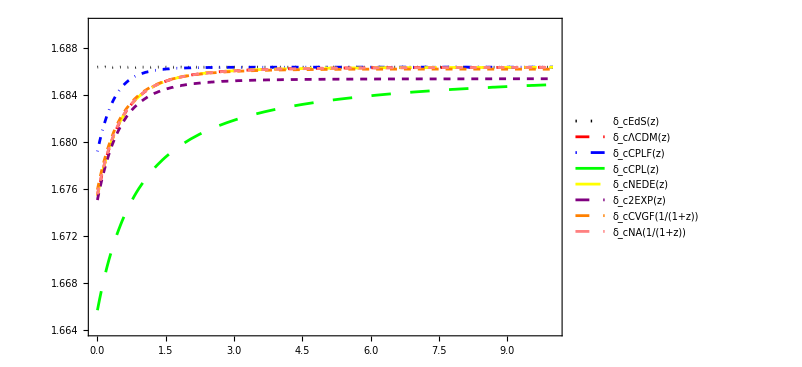

```mathematica
Plot[{Subscript[δ, cEdS][z], Subscript[δ, cΛCDM][z], Subscript[δ, cCPLF][z], Subscript[δ, cCPL][z], Subscript[δ, cNEDE][z], Subscript[δ, c2EXP][z], Subscript[δ, cCVGF][1/(1+z)], Subscript[δ, cNA][1/(1+z)]}, {z,0,10}, PlotRange->{{0,10},{1.664,1.69}},Frame->True,ImageSize->5*260/3.54*{GoldenRatio,1}, PlotStyle->{ Directive[Thick, Black, Dotted], Directive[Thick, Red, Dashed], Directive[Thick, Blue, DotDashed], Directive[ Green, Dashing[Large]], Directive[ Yellow, Dashing[Medium]], Directive[ Purple, Dashing[Small]], Directive[ Orange, Dashing[Small]], Directive[ Pink, Dashing[Small]]}, PlotLegends->"Expressions"]
```

```mathematica
(*FrameTicks->{{Automatic,Automatic},{Table[{10^i,DisplayForm@SuperscriptBox[10,i]},{i,-1,6,2}],Automatic}}*)
```

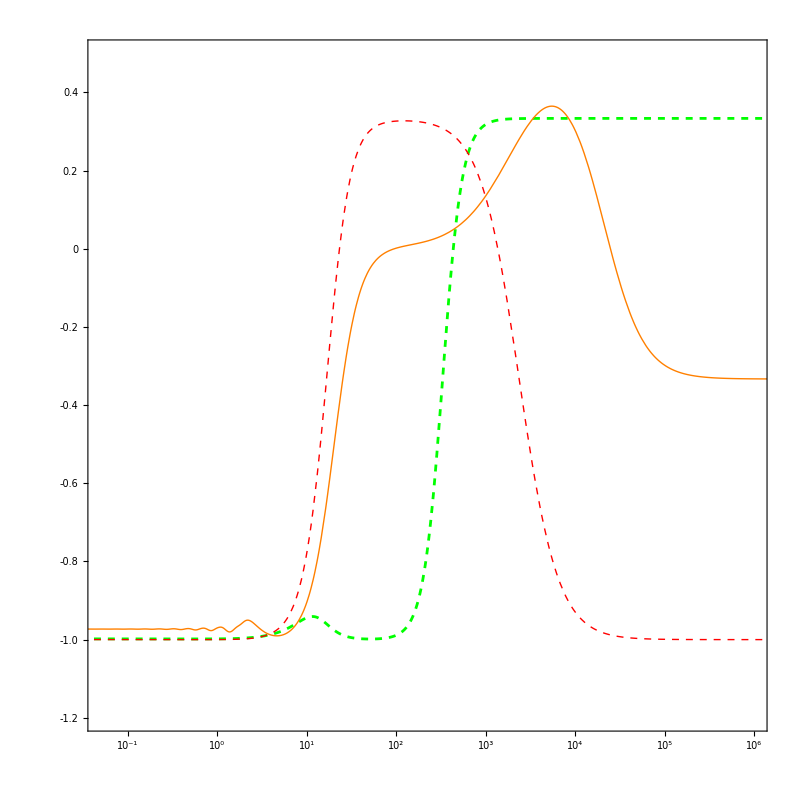

```mathematica
Plot[{Subscript[w, NA][z], Subscript[w, CVGF][z], Subscript[w, 2F][z]}, {z,0.01,10^7}, 
PlotRange->{{0.05,10^6},{-1.2,0.5}},
Frame->True,Axes->False,FrameTicks->{{Automatic,Automatic},{Table[{10^i,DisplayForm@SuperscriptBox[10,i]},{i,-1,6,1}],Automatic}},
ImageSize->5*350/3.54*{GoldenRatio,1},AspectRatio->1,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->18}, ScalingFunctions->{"Log","Linear"},
FrameLabel->(MaTeX[#,Magnification->1.7]&)/@{"z_{r} +1", "w(z)"},
PlotStyle->{ Directive[ Green, Dashing[Small]], 
Directive[Thick, Red, Dashed], 
Directive[Thick, Orange]}, 
PlotLegends->Placed[LineLegend[{
Directive[Thick, Green, Dashing[Small]],
Directive[Thick, Red,Dashed], 
Directive[Thick, Orange]}, 
{(MaTeX[#,Magnification->1.3]&)/@Style["NA"],
(MaTeX[#,Magnification->1.3]&)/@Style["CVGF"], 
(MaTeX[#,Magnification->1.3]&)/@Style["2F"]}, 
LegendMarkerSize->25,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&), LegendLayout->{"Column",1},LabelStyle->{Black,Bold,12}],{{0.03,0.65},{0,0}}](*, Epilog-> Inset[Plot[Subscript[w, 2F][a],{a, 0.01,10^7}, Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},FrameTicks->None,PlotRange->{{0.01,10},{-1.,-0.94}}],{1,-0.4}]*)]
```

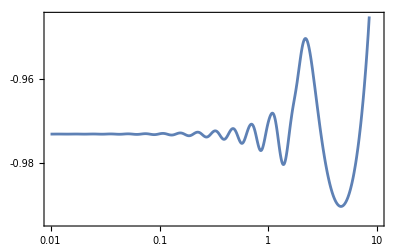

```mathematica
Plot[Subscript[w, 2F][a],{a, 0.01,10^7}, Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},FrameTicks->Automatic,PlotRange->{{0.01,10},{-0.994,-0.945}}]
```

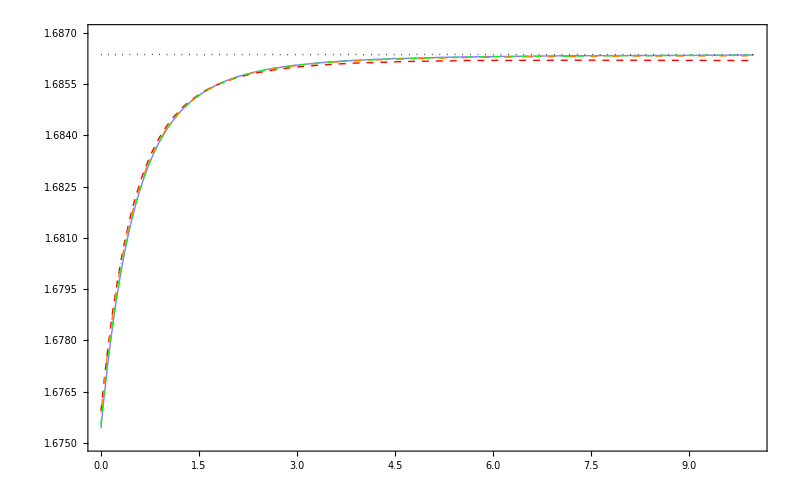

```mathematica
Plot[{Subscript[δ, cEdS][z], Subscript[δ, cΛCDM][z],Subscript[δ, cCVGF][1/(1+z)], Subscript[δ, cNA][1/(1+z)],Subscript[δ, c2F][1/(1+z)]}, {z,0,10},
Frame->True,Axes->False, ImageSize->5*350/3.54*{GoldenRatio,1},FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->18},FrameLabel->(MaTeX[#,Magnification->1.7]&)/@{"z", "\\delta_{c}(z)"}, 
PlotStyle->{ Directive[Thick, Black, Dotted],
Directive[Thick, Blue,Opacity[0.5]],
Directive[Thick, Red,Dashed], 
Directive[Thick, Green,Dashing[Small]], 
Directive[Thick, Orange,DotDashed]}, 
PlotRange->{{0, 10},{1.675, 1.687}}, 
PlotLegends->Placed[LineLegend[{
Directive[Thick, Black, Dotted],
Directive[Thick, Blue,Opacity[0.5]],
Directive[Thick, Red,Dashed], 
Directive[Thick, Green,Dashing[Small]], 
Directive[Thick, Orange, DotDashed]}, 
{(MaTeX[#,Magnification->1.3]&)/@Style["EdS"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\Lambda CDM"],
(MaTeX[#,Magnification->1.3]&)/@Style["CVGF"], 
(MaTeX[#,Magnification->1.3]&)/@Style["NA"], 
(MaTeX[#,Magnification->1.3]&)/@Style["2F"]}, 
LegendMarkerSize->25,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&), LegendLayout->{"Column",1},LabelStyle->{Black,Bold,12}],{{0.8,0.2},{0,0}}]]
```